```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<Teukolsky`
```

```mathematica
Initψout[l_,m_,kout_,a_,M_,r0_] := 
Module[{i = l, j= m , N=kout, s = a, Μ=M, ρ0 = r0, f0,f1,f2,f3,f4,f5,f6,n,ω,rp,rm,λ,Q = SpinWeightedSpheroidalEigenvalue},
rp= Μ+√(Μ^2-s^2);
rm = Μ-√(Μ^2-s^2);
ω = j/Μ(Μ/ρ0)^(3/2)/(1+(s/Μ)(Μ/ρ0)^(3/2));
f0= -2 ⅈ n ω;
f1=n^2-λ+ω (-4 ⅈ Μ+s^2 ω)+n (-1+4 ⅈ Μ ω);
f2=-2 ⅈ s^2 (-2+n) ω+2Μ (-3+5 n-2 n^2+λ-2 s j ω+s^2 ω^2);
f3=4 Μ^2 (-2+n)^2+s^2 (8+j^2-8 n+2 n^2-λ);
f4=-2 a^2 Μ (15-11 n+2 n^2);
f5=s^4 (12-7 n+n^2);
λ = Q[0,i,j,s ω]-(s ω)^2+2 j s ω;

cs = RecurrenceTable[{f0 c[n]+f1 c[n-1]+f2 c[n-2]+f3 c[n-3]+f4 c[n-4]+f5 c[n-5]==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0},c,{n,0,N}]
]
ψout[l_,m_,kout_,a_,M_,r0_,r_,c_]:=Exp[ⅈ m/M 1/((r0/M)^(3/2)+a/M) (r+M Log[(r^2-2 M r +a^2)/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]Sum[c[[n]] r^-n,{n,1,kout}]
```

```mathematica
Initψin[l_,m_,kin_,a_,M_,r0_] := 
Module[{i = l, j= m , N=kin, s = a, Μ=M, ρ0 = r0,f,k,ω,γ,rp,rm,λ,Q = SpinWeightedSpheroidalEigenvalue},
rp= Μ+√(Μ^2-s^2);
rm = Μ-√(Μ^2-s^2);
ω = j/Μ(Μ/ρ0)^(3/2)/(1+(s/Μ)(Μ/ρ0)^(3/2));
γ = (2Μ rp ω-s j)/rp^2;
λ = Q[0,i,j,s ω]-(s ω)^2+2 j s ω;
f= {s^4 (2-3 k+k^2)-4 s j Μ rp^3 ω+s^2 rp (rp (2+12 k^2+j^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+Μ (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) Μ^2+2 Μ rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))),2 (-6 s j Μ rp^2 ω+s^2 (rp (13+4 k^2+j^2+6 ⅈ rp γ+k (-15-6 ⅈ rp γ)-λ+2 rp^2 ω^2)+Μ (-10+9 k-2 k^2+3 rp^2 ω^2))+rp ((26-30 k+8 k^2) Μ^2+Μ rp (-49-20 k^2-20 ⅈ rp γ+k (66+20 ⅈ rp γ)+3 λ)+rp^2 (20+10 k^2+15 ⅈ rp γ+k (-30-15 ⅈ rp γ)-2 λ-3 rp^2 (γ^2-ω^2)))),4 (-3+k)^2 Μ^2+2 Μ rp (-71-10 k^2-40 ⅈ rp γ+k (54+20 ⅈ rp γ)+3 λ)-12 s j Μ rp ω+s^2 (18+2 k^2+j^2+16 ⅈ rp γ+k (-12-8 ⅈ rp γ)-λ+6 Μ rp ω^2+6 rp^2 ω^2)+rp^2 (90+15 k^2+80 ⅈ rp γ+k (-75-40 ⅈ rp γ)-6 λ-15 rp^2 (γ^2-ω^2)),2 (-ⅈ s^2 (-3+k) γ-15 ⅈ (-3+k) rp^2 γ-10 rp^3 (γ^2-ω^2)+Μ (-28-2 k^2-30 ⅈ rp γ+5 k (3+2 ⅈ rp γ)+λ-2 s j ω+s^2 ω^2)+rp (36-21 k+3 k^2-2 λ+2 s^2 ω^2)),4+(-4+k)^2-k+4 ⅈ (-4+k) Μ γ-12 ⅈ (-4+k) rp γ-λ+s^2 ω^2-15 rp^2 (γ^2-ω^2),-2 ⅈ (-5+k) γ-6 rp γ^2+6 rp ω^2,-γ^2+ω^2};

cs = RecurrenceTable[{c[k] f⟦1⟧+c[-1+k] f⟦2⟧+c[-2+k] f⟦3⟧+c[-3+k] f⟦4⟧+c[-4+k] f⟦5⟧+c[-5+k] f⟦6⟧+c[-6+k] f⟦7⟧==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0,c[-5]==0},c,{k,0,N}]
]
ψin[l_,m_,kin_,a_,M_,r0_,r_,c_]:=Exp[-ⅈ ((2M(M+√(M^2-a^2))(m/M(M/r0)^(3/2)/(1+(a/M)(M/r0)^(3/2)))-a m)/((M+√(M^2-a^2))^2)) (r+M Log[(r^2-2 M r +a^2)/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]Sum[c[[n+1]](r-M-√(M^2-a^2))^n,{n,0,kin}]
```

```mathematica
rs[r_]:=r+M Log[((r-M-√(M^2-a^2))(r-M+√(M^2-a^2)))/M^2] +(2 M^2-a^2)/(2 √(M^2-a^2)) Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))];
```

```mathematica
l=2;
m=2;

M=1`32;
a=.998`32M;
rp =M+√(M^2-a^2);
rout=(1`32)10^5 M;
rin = (1`32)10^-5 M+rp;
r0=10`32M;
kout=1000;
kin=1000;

ω = m/M 1/((r0/M)^(3/2)+a/M);
γ =a ω;
λ = SpinWeightedSpheroidalEigenvalue[0,l,m,a ω]-γ^2+2m γ;

Δ[r_]:=r^2-2M r+a^2;
W[r_]:=(((r^2+a^2)ω-a m)/r^2)^2-Δ[r]/r^4(λ-2 a m ω +a^2 ω^2+(2(M r-a^2))/r^2)

Outcs = Initψout[l,m,kout,a,M,r0];
Incs = Initψin[l,m,kin,a,M,r0];

OuterBoundary=ψout[l,m,kout,a,M,r0,rout,Outcs]
InnerBoundary=ψin[l,m,kin,a,M,r0,rin,Incs]


OuterDeriv = D[ψout[l,m,kout,a,M,r0,r,Outcs],r]/.{r->rout}
InnerDeriv = D[ψin[l,m,kin,a,M,r0,r,Incs],r]/.{r->rin}
```

0.9963693969226913165929664883+0.085135801084901704945464087 ⅈ

0.997692067429260631037953+0.06805212966149240658431 ⅈ

-0.005219832629325572443525987+0.06108924121045654720395394249 ⅈ

-100411.7078837653779328+1.47212133741665933966485×10^6 ⅈ

```mathematica
Nψin=ψ/.NDSolve[{Δ[r]^2/r^4 ψ''[r]+(2Δ[r](r^2(r-M)-Δ[r]r))/r^6 ψ'[r]+W[r]ψ[r]==0,ψ'[rin]==InnerDeriv,ψ[rin]==InnerBoundary},ψ,{r,rin,r0}][[1]];
Nψout=ψ/.NDSolve[{Δ[r]^2/r^4 ψ''[r]+(2Δ[r](r^2(r-M)-Δ[r]r))/r^6 ψ'[r]+W[r]ψ[r]==0,ψ'[rout]==OuterDeriv,ψ[rout]==OuterBoundary},ψ,{r,rout,r0}][[1]];
```

```mathematica
q=1;
v=√(M/r0);
ℰ=(1-2 v^2+a/M v^3)/(√(1-3 v^2+2 a/M v^3));
ℒ=r0 v (1-2 a/M v^3+(a/M)^2 v^4)/(√(1-3 v^2+2 a/M v^3));
gtt = -(r0^3+a^2 (2 M+r0))/(r0 (a^2+r0 (-2 M+r0)));
gtϕ = -(2 a M)/(a^2 r0-2 M r0^2+r0^3);
ut = gtϕ ℒ-gtt ℰ;
α = (-4π q r0)/(ut Δ[r0])SpinWeightedSpheroidalHarmonicS[0,l,m,a ω,π/2,0]
cHor = α Nψout[r0]/(Nψin[r0]Nψout'[r0]-Nψout[r0]Nψin'[r0]);
```

-0.507489705107567312415176407062

```mathematica
cInf = cHor Nψin[r0]/Nψout[r0];
```

```mathematica
orbit = KerrGeoOrbit[a,r0,0,1];
mode= TeukolskyPointParticleMode[0,l,m,0,0,orbit];
BHPTUp = mode["Amplitudes"]["ℐ"];
BHPTIn = mode["Amplitudes"]["ℋ"];
```

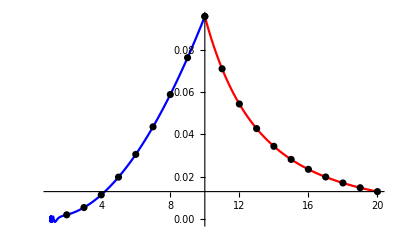

```mathematica
Show[Plot[{Re[cInf Nψout[r]/r]},{r,r0,20},PlotStyle->{Red},PlotRange->All],
Plot[{Re[cHor Nψin[r]/r]},{r,rin,r0},PlotStyle->{Blue}],
ListPlot[Table[{r,Re[BHPTUp TeukolskyRadial[0,l,m,a,ω]["Up"][r]]},{r,10,20,1}],PlotStyle->{Black}],
ListPlot[Table[{r,Re[BHPTIn TeukolskyRadial[0,l,m,a,ω]["In"][r]]},{r,2,10,1}],PlotStyle->{Black}],
PlotRange->All]
```

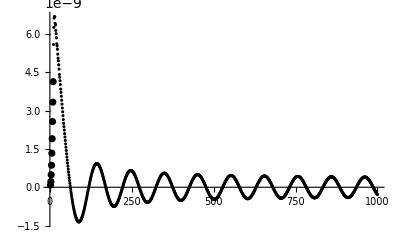

```mathematica
Show[
ListPlot[Table[{r,Re[BHPTUp TeukolskyRadial[0,l,m,a,ω]["Up"][r]]-Re[cInf Nψout[r]/r]},{r,10,1000,1}],PlotStyle->{Black}],
ListPlot[Table[{r,Re[BHPTIn TeukolskyRadial[0,l,m,a,ω]["In"][r]]-Re[cHor Nψin[r]/r]},{r,2,10,1}],PlotStyle->{Black}],
PlotRange->All]
```

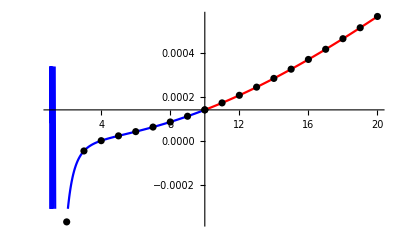

```mathematica
Show[
Plot[{Im[cInf Nψout[r]/r]},{r,r0,20},PlotStyle->{Red},PlotRange->All],
Plot[{Im[cHor Nψin[r]/r]},{r,rin,r0},PlotStyle->{Blue}],
ListPlot[Table[{r,Im[BHPTUp TeukolskyRadial[0,l,m,a,ω]["Up"][r]]},{r,10,20,1}],PlotStyle->{Black}],
ListPlot[Table[{r,Im[BHPTIn TeukolskyRadial[0,l,m,a,ω]["In"][r]]},{r,2,10,1}],PlotStyle->{Black}],
PlotRange->All]
```

```mathematica
cInf 
BHPTUp

cHor 
BHPTIn
```

-0.0885459+0.0401146 ⅈ

-0.091663561842423036+0.03245040196465867 ⅈ

-0.000679266+0.00110455 ⅈ

0.0006965159429681208+0.0010011453635826997 ⅈ

```mathematica
Abs[cInf]/Abs[BHPTUp]
Abs[cHor]/Abs[BHPTIn]
```

0.9997

1.06321

```mathematica
7956.21245077051
```

7956.21

```mathematica
12166.395276039795
```

12166.4